```mathematica
Quit[];
```

```mathematica
<<FeynArts`
<<FormCalc`
```

FeynArts 3.11 (2 Sep 2019)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.9 (6 Oct 2019)

by Thomas Hahn

```mathematica
(* Create my topologies. *)
(* 0 loops, 2 incoming legs, 2 outgoing legs.*)
topologies=CreateTopologies[0,1 -> 2];
_Hel=0;
Print[topologies];
```

TopologyList[Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][4]],Propagator[Outgoing][Vertex[1][2],Vertex[3][4]],Propagator[Outgoing][Vertex[1][3],Vertex[3][4]]]]

loading generic model file /Users/kpachal/Code/DMSP/FormCalc/FeynArts-3.11/Models/DMsimp_s_spin1_vector.gen

> $GenericMixing is OFF

generic model {DMsimp_s_spin1_vector} initialized

loading classes model file /Users/kpachal/Code/DMSP/FormCalc/FeynArts-3.11/Models/DMsimp_s_spin1_vector.mod

> 46 particles (incl. antiparticles) in 26 classes

> $CounterTerms are ON

> 147 vertices

> 48 counterterms of order 1

classes model {DMsimp_s_spin1_vector} initialized

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

in total: 1 Classes insertion

> Top. 1 ad/bdcd/0.m, 0 diagrams

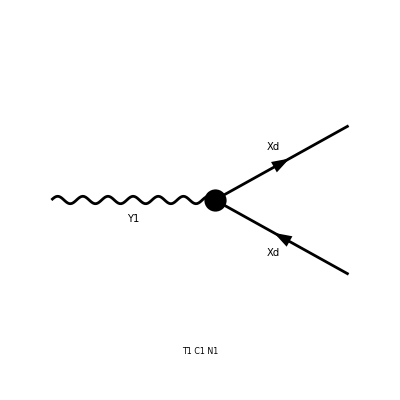

```mathematica
(* Z' to DM *)
diagvec=InsertFields[topologies,{V[5]}->{F[13],-F[13]},InsertionLevel->{Classes},
Model->"DMsimp_s_spin1_vector",
GenericModel->"DMsimp_s_spin1_vector"];
Paint[diagvec];
```

```mathematica
ClearProcess[];
amplist = CreateFeynAmp[diagvec];
Print[amplist];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

FeynAmpList[Process→{{V[5],p1,MY1,{}}}→{{F[13],k1,MXd,{}},{-F[13],k2,MXd,{}}},Model→{DMsimp_s_spin1_vector},GenericModel→{DMsimp_s_spin1_vector},AmplitudeLevel→{Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][FeynAmp[GraphID[Topology==1,Generic==1,Classes==1,Number==1],Integral[],ⅈ ū[k1,MXd].(ⅈ gc76 ga[Lor1].(omSubscript[-])+ⅈ gc76 ga[Lor1].(omSubscript[+])).v[k2,MXd] ep[V[5],p1,Lor1]]]

```mathematica
amp=CalcFeynAmp[amplist,FermionChains->VA];
```

preparing FORM code in /Users/kpachal/fc-amp-9.frm

running FORM...

ok

```mathematica
(* Done with FeynArts! Time to pass the amplitude to FormCalc. *)
(* Squared matrix elements; evaluate *)
squared = SquaredME[amp];
Print[squared];
```

{FF[F1] FFC[F1] Mat[F1,F1],{FF[F1]→-gc76,FFC[F1]→-(gc76Superscript[*])}}

```mathematica
(* SquaredME returns a list of {squared, squaredRules}, where we should later apply "squaredRules" to "squared". *)
cleanSquaredME = squared[[1]]//.squared[[2]]//.HelicityME[amp]//FullSimplify
```

> 1 helicity matrix elements

preparing FORM code in /Users/kpachal/fc-hel-9.frm

running FORM...

ok

1/2 gc76 (Abb1+2 MXd^2) (gc76Superscript[*])

```mathematica
(* Expand Abb1 *)
expanded = cleanSquaredME//.Abbr[]
```

1/2 gc76 (gc76Superscript[*]) (MY1^2-4 Pair[e[1],k[2]] Pair[ec[1],k[2]])

```mathematica
(* The e and ec in here are the Z' polarisation vector and its conjugate. *)
(* We want to sum over polarisations and make them go away: *)
TotalME = PolarizationSum[cleanSquaredME]//.Subexpr[]//.Abbr[]
```

preparing FORM code in /Users/kpachal/fc-pol-9.frm

running FORM...

ok

gc76 (2 MXd^2+MY1^2) (gc76Superscript[*])

```mathematica
(* This is our matrix element. Now to compute widths. *)
(* Golden rule: Gamma = pStar/(32 Pi^2 MY1^2) int Msquared dOmega *)
(* and int dOmega = 2 pi int dCosTheta from -1 to 1 *)
MEIntegral = 2 Pi Integrate[TotalME, {CosTheta,-1,1}]
Width = pStar/(32 Pi^2 MY1^2) MEIntegral
```

4 gc76 (2 MXd^2+MY1^2) π (gc76Superscript[*])

(gc76 (2 MXd^2+MY1^2) pStar (gc76Superscript[*]))/(8 MY1^2 π)

```mathematica
(* Use the vertex replacement list from the model file to get vertices we recognize *)
FinalVertices = Width//. M$FACouplings
```

(gVXd (2 MXd^2+MY1^2) pStar (gVXdSuperscript[*]))/(8 MY1^2 π)

```mathematica
(* Finally format for us *)
Clean = FinalVertices//.{pStar-> 1/2  Sqrt[MY1^2 - 4 MXd^2]  , MXd-> Sqrt[MY1^2 zDM]}//FullSimplify
```

(gVXd √(MY1^2 (1-4 zDM)) (1+2 zDM) (gVXdSuperscript[*]))/(16 π)

```mathematica
(* Validated against known result from LHC DM WG: *)
(* This is correct less the factor of 16 versus 12 in the denominator. *)
(* Suspect that is due to average over polarisation states *)
```